## Brian Martin Ess 288 Final

```mathematica
CurrentFolder=NotebookDirectory[]
```

C:\Users\Brian\Desktop\ESS288Final-main\Final Project\

```mathematica
TargetFile = StringJoin[CurrentFolder,"VehiclesClean6.csv"];
```

```mathematica
AllDate = Import[TargetFile,"Dataset","HeaderLines"->1]
```

```mathematica
years = Range[1986,2018];
```

```mathematica
ToyotaAvgMpg = List[21.66666667,22.71428571,23.875,21.83333333,22.83333333,22.33333333,22.14285714,22.66666667,23,23.57142857,23.85714286,23.85714286,23.57142857,24.14285714,25,27.85714286,28,28.28571429,29,29.28571429,29.4,29.66666667,29.66666667,29.8,31.8,31.4,34.66666667,35.16666667,35.42857143,35.42857143,38.25,36.75,36.92857143];
GasPrices = List[1.078,1.158,1.245,1.244,1.072,1.176,1.523,1.46,1.386,1.603,1.895,2.314,2.618,2.843,3.299,2.406,2.835,3.576,3.68,3.575,3.437,2.52,2.25,2.528,2.813];
years2 = Range[1994,2018];
```

```mathematica
ToyotaData =Transpose[{years,ToyotaAvgMpg}]
```

{{1986,21.6667},{1987,22.7143},{1988,23.875},{1989,21.8333},{1990,22.8333},{1991,22.3333},{1992,22.1429},{1993,22.6667},{1994,23},{1995,23.5714},{1996,23.8571},{1997,23.8571},{1998,23.5714},{1999,24.1429},{2000,25},{2001,27.8571},{2002,28},{2003,28.2857},{2004,29},{2005,29.2857},{2006,29.4},{2007,29.6667},{2008,29.6667},{2009,29.8},{2010,31.8},{2011,31.4},{2012,34.6667},{2013,35.1667},{2014,35.4286},{2015,35.4286},{2016,38.25},{2017,36.75},{2018,36.9286}}

```mathematica
GasData = Transpose[{years2,GasPrices}]
```

{{1994,1.078},{1995,1.158},{1996,1.245},{1997,1.244},{1998,1.072},{1999,1.176},{2000,1.523},{2001,1.46},{2002,1.386},{2003,1.603},{2004,1.895},{2005,2.314},{2006,2.618},{2007,2.843},{2008,3.299},{2009,2.406},{2010,2.835},{2011,3.576},{2012,3.68},{2013,3.575},{2014,3.437},{2015,2.52},{2016,2.25},{2017,2.528},{2018,2.813}}

```mathematica
lm = LinearModelFit[ToyotaData,x,x]
```

FittedModel[-1011.77+0.519364 x]

```mathematica
lm["RSquared"]
```

0.923298

```mathematica
PointSizeX=5;
PaddingX=1.1;
```

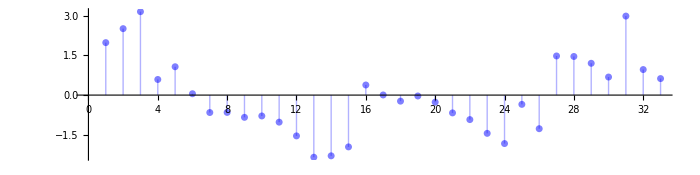

```mathematica
resid = ListPlot[lm["FitResiduals"], Filling->Axis,PlotStyle->Directive[Blue,Opacity[0.5],AbsolutePointSize[PointSizeX]],LabelStyle -> Directive[Black,FontFamily-> "Helvetica",FontSize->10],ImageSize->700,AspectRatio->1/4]
```

```mathematica
Export["C:\\Users\\Brian\\Desktop\\ESS288Final-main\\Final Project\\Resid.PDF",resid]
```

C:\Users\Brian\Desktop\ESS288Final-main\Final Project\Resid.PDF

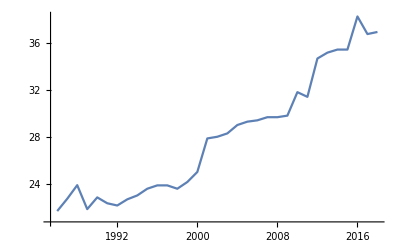

```mathematica
ListLinePlot[ToyotaData]
```

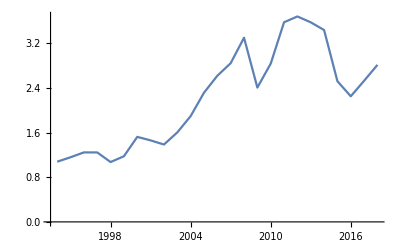

```mathematica
ListLinePlot[GasData]
```

```mathematica
CombinePlots
```

```mathematica
lm2 = LinearModelFit[GasData,x,x]
```

-195.405

```mathematica
TwoAxisPlot[{f_,g_},{x_,x1_,x2_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[Plot[#,{x,x1,x2},Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];{frange,grange}=(PlotRange/. AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/. Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
```

```mathematica
TwoAxisPlot[{ToyotaData[x],GasData[x]},{x,1990,2018}]
```